```mathematica
∫_0^(2 Pi) Sin[4 x^2]ⅆx
```

1/2 √(π/2) FresnelS[4 √(2 π)]

```mathematica
∫Cos[5 x]Sin[4 x]Exp[I 2 x^2]ⅆx
```

(1/16+ⅈ/16) ⅇ^(-(81 ⅈ)/8) √π (ⅇ^(10 ⅈ) Erfi[(1/4+ⅈ/4)-(1+ⅈ) x]-Erfi[(9/4+(9 ⅈ)/4)-(1+ⅈ) x]+ⅇ^(10 ⅈ) Erfi[(1/4+ⅈ/4)+(1+ⅈ) x]-Erfi[(9/4+(9 ⅈ)/4)+(1+ⅈ) x])

```mathematica
ExpToTrig[Exp[2I (x+4x^2)]]
```

Cos[2 x+8 x^2]+ⅈ Sin[2 x+8 x^2]

```mathematica
FullSimplify[Cos[2 x+8 x^2]+ⅈ Sin[2 x+8 x^2]]
```

ⅇ^(2 ⅈ x (1+4 x))

```mathematica
FullSimplify[Log[x+ 2 I Sin[6 x]]]
```

Log[x+2 ⅈ Sin[6 x]]

```mathematica
∫ Simplify[Log[x+ 2 I Sin[6 x]]]ⅆx
```

$Aborted

```mathematica
∫ Log[ 2 I Sin[6 x]]ⅆx
```

-x Log[1-ⅇ^(12 ⅈ x)]+x Log[2 ⅈ Sin[6 x]]+1/12 ⅈ (36 x^2+PolyLog[2,ⅇ^(12 ⅈ x)])

```mathematica
ref:=(r1-r2 Exp[I f])/(1-r1 r2 Exp[I f])
r1:=0.9876
r2:=0.9852
ans:=Table[{f,Abs[ref]^2}, {f,-0.8,0.8,0.01}]
ans
```

{{-0.8,0.998775},{-0.79,0.998745},{-0.78,0.998714},{-0.77,0.998683},{-0.76,0.998649},{-0.75,0.998615},{-0.74,0.998579},{-0.73,0.998542},{-0.72,0.998503},{-0.71,0.998462},{-0.7,0.99842},{-0.69,0.998376},{-0.68,0.99833},{-0.67,0.998282},{-0.66,0.998231},{-0.65,0.998178},{-0.64,0.998123},{-0.63,0.998065},{-0.62,0.998005},{-0.61,0.997941},{-0.6,0.997874},{-0.59,0.997804},{-0.58,0.99773},{-0.57,0.997652},{-0.56,0.99757},{-0.55,0.997483},{-0.54,0.997392},{-0.53,0.997295},{-0.52,0.997193},{-0.51,0.997084},{-0.5,0.99697},{-0.49,0.996848},{-0.48,0.996718},{-0.47,0.99658},{-0.46,0.996433},{-0.45,0.996276},{-0.44,0.996109},{-0.43,0.995929},{-0.42,0.995737},{-0.41,0.99553},{-0.4,0.995308},{-0.39,0.995069},{-0.38,0.994811},{-0.37,0.994532},{-0.36,0.994229},{-0.35,0.9939},{-0.34,0.993542},{-0.33,0.993151},{-0.32,0.992723},{-0.31,0.992254},{-0.3,0.991738},{-0.29,0.991168},{-0.28,0.990536},{-0.27,0.989834},{-0.26,0.989051},{-0.25,0.988173},{-0.24,0.987185},{-0.23,0.986068},{-0.22,0.984798},{-0.21,0.983346},{-0.2,0.981677},{-0.19,0.979744},{-0.18,0.97749},{-0.17,0.97484},{-0.16,0.971697},{-0.15,0.967932},{-0.14,0.963371},{-0.13,0.957777},{-0.12,0.95082},{-0.11,0.942028},{-0.1,0.930716},{-0.09,0.915855},{-0.08,0.895864},{-0.07,0.868234},{-0.06,0.828875},{-0.05,0.770978},{-0.04,0.683296},{-0.03,0.548972},{-0.02,0.352918},{-0.01,0.124588},{0.,0.0078916},{0.01,0.124588},{0.02,0.352918},{0.03,0.548972},{0.04,0.683296},{0.05,0.770978},{0.06,0.828875},{0.07,0.868234},{0.08,0.895864},{0.09,0.915855},{0.1,0.930716},{0.11,0.942028},{0.12,0.95082},{0.13,0.957777},{0.14,0.963371},{0.15,0.967932},{0.16,0.971697},{0.17,0.97484},{0.18,0.97749},{0.19,0.979744},{0.2,0.981677},{0.21,0.983346},{0.22,0.984798},{0.23,0.986068},{0.24,0.987185},{0.25,0.988173},{0.26,0.989051},{0.27,0.989834},{0.28,0.990536},{0.29,0.991168},{0.3,0.991738},{0.31,0.992254},{0.32,0.992723},{0.33,0.993151},{0.34,0.993542},{0.35,0.9939},{0.36,0.994229},{0.37,0.994532},{0.38,0.994811},{0.39,0.995069},{0.4,0.995308},{0.41,0.99553},{0.42,0.995737},{0.43,0.995929},{0.44,0.996109},{0.45,0.996276},{0.46,0.996433},{0.47,0.99658},{0.48,0.996718},{0.49,0.996848},{0.5,0.99697},{0.51,0.997084},{0.52,0.997193},{0.53,0.997295},{0.54,0.997392},{0.55,0.997483},{0.56,0.99757},{0.57,0.997652},{0.58,0.99773},{0.59,0.997804},{0.6,0.997874},{0.61,0.997941},{0.62,0.998005},{0.63,0.998065},{0.64,0.998123},{0.65,0.998178},{0.66,0.998231},{0.67,0.998282},{0.68,0.99833},{0.69,0.998376},{0.7,0.99842},{0.71,0.998462},{0.72,0.998503},{0.73,0.998542},{0.74,0.998579},{0.75,0.998615},{0.76,0.998649},{0.77,0.998683},{0.78,0.998714},{0.79,0.998745},{0.8,0.998775}}

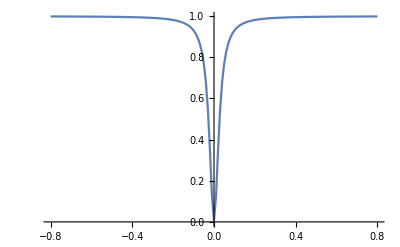

```mathematica
ListLinePlot[ans, PlotRange->All]
```